```mathematica
PhiEvolution[name_,maxIt_]:=Module[{dirOut,betaMeans,thetaMeans,sigmaMeans,rhoMeans,dir,obsItem,obsUser,xMeans,wMeans},
dirOut="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/output/";
SetDirectory[dirOut<>name];

betaMeans=Import["betaMeans.tsv"];
thetaMeans=Import["thetaMeans.tsv"];
sigmaMeans=Import["sigmaMeans.tsv"];
rhoMeans=Import["rhoMeans.tsv"];

dir="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/";
SetDirectory[dir];

obsItem=Import["obsItem.tsv"];
obsUser=Import["obsUser.tsv"];

xMeans=Mean[obsItem[[;;,2;;]]];
wMeans=Mean[obsUser[[;;,2;;]]];

(*ListPlot[Join[betaMeans[[;;,1]]*thetaMeans[[;;,1]],sigmaMeans[[;;,1]]*xMeans,rhoMeans0[[;;,1]]*wMeans],Joined->True,PlotRange->All]*)
Manipulate[ListPlot[Join[betaMeans[[;;,i]]*thetaMeans[[;;,i]],sigmaMeans[[;;,i]]*xMeans,rhoMeans[[;;,i]]*wMeans],Joined->True,PlotRange->All,GridLines->{{25.5,75.5}}],{i,1,maxIt+2,1}]
]
PhiEvolutionB[name_,maxIt_]:=Module[{dirOut,betaMeans,thetaMeans,sigmaMeans,rhoMeans,dir,obsItem,obsUser,xMeans,wMeans,xiMeans,etaMeans},
dirOut="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/output/";
SetDirectory[dirOut<>name];

betaMeans=Import["betaMeans.tsv"];
thetaMeans=Import["thetaMeans.tsv"];
sigmaMeans=Import["sigmaMeans.tsv"];
rhoMeans=Import["rhoMeans.tsv"];
xiMeans=Import["xiMeans.tsv"];
xiMeans=xiMeans[[;;,1]];
etaMeans=Import["etaMeans.tsv"];
etaMeans=etaMeans[[;;,1]];

dir="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/";
SetDirectory[dir];

obsItem=Import["obsItem.tsv"];
obsUser=Import["obsUser.tsv"];

xMeans=Mean[obsItem[[;;,2;;]]];
wMeans=Mean[obsUser[[;;,2;;]]];

(*Print[xiMeans[[1]]];
Print[etaMeans[[1]]];*)

(*ListPlot[Join[betaMeans[[;;,1]]*thetaMeans[[;;,1]],sigmaMeans[[;;,1]]*xMeans,rhoMeans0[[;;,1]]*wMeans],Joined->True,PlotRange->All]*)
Manipulate[ListPlot[Join[betaMeans[[;;,i]]*thetaMeans[[;;,i]],sigmaMeans[[;;,i]]*xMeans/etaMeans[[i]],rhoMeans[[;;,i]]*wMeans/xiMeans[[i]]],Joined->True,PlotRange->All,GridLines->{{25.5,75.5}}],{i,1,maxIt+2,1}]
]
PhiEvolution[name_,maxIt_,k_]:=Module[{dirOut,betaMeans,thetaMeans,sigmaMeans,rhoMeans,dir,obsItem,obsUser,xMeans,wMeans},
dirOut="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/output/";
SetDirectory[dirOut<>name];

betaMeans=Import["betaMeans.tsv"];
thetaMeans=Import["thetaMeans.tsv"];
sigmaMeans=Import["sigmaMeans.tsv"];
rhoMeans=Import["rhoMeans.tsv"];

dir="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/";
SetDirectory[dir];

obsItem=Import["obsItem.tsv"];
obsUser=Import["obsUser.tsv"];

xMeans=Mean[obsItem[[;;,2;;]]];
wMeans=Mean[obsUser[[;;,2;;]]];

(*ListPlot[Join[betaMeans[[;;,1]]*thetaMeans[[;;,1]],sigmaMeans[[;;,1]]*xMeans,rhoMeans0[[;;,1]]*wMeans],Joined->True,PlotRange->All]*)
Manipulate[ListPlot[Join[betaMeans[[;;,i]]*thetaMeans[[;;,i]],sigmaMeans[[;;,i]]*xMeans,rhoMeans[[;;,i]]*wMeans],Joined->True,PlotRange->All,GridLines->{{k+.5,k+50.5}}],{i,1,maxIt+2,1}]
]
PhiEvolutionLatents[name_,maxIt_,k_]:=Module[{dirOut,betaMeans,thetaMeans,sigmaMeans,rhoMeans,dir,obsItem,obsUser,xMeans,wMeans,list},
dirOut="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/output/";
SetDirectory[dirOut<>name];

betaMeans=Import["betaMeans.tsv"];
thetaMeans=Import["thetaMeans.tsv"];
sigmaMeans=Import["sigmaMeans.tsv"];
rhoMeans=Import["rhoMeans.tsv"];

dir="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/";
SetDirectory[dir];

obsItem=Import["obsItem.tsv"];
obsUser=Import["obsUser.tsv"];

xMeans=Mean[obsItem[[;;,2;;]]];
wMeans=Mean[obsUser[[;;,2;;]]];

(*ListPlot[Join[betaMeans[[;;,1]]*thetaMeans[[;;,1]],sigmaMeans[[;;,1]]*xMeans,rhoMeans0[[;;,1]]*wMeans],Joined->True,PlotRange->All]*)

Manipulate[
list = Join[betaMeans[[;;,i]]*thetaMeans[[;;,i]]];
ListPlot[list,Joined->True,GridLines->{{k+.5,k+50.5}},PlotRange->{0,Max[list]}],{i,1,maxIt+2,1}]
]
PhiEvolutionF25[name_,maxIt_,k_]:=Module[{dirOut,betaMeans,thetaMeans,sigmaMeans,rhoMeans,dir,obsItem,obsUser,xMeans,wMeans},
dirOut="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/output/";
SetDirectory[dirOut<>name];

betaMeans=Import["betaMeans.tsv"];
thetaMeans=Import["thetaMeans.tsv"];
sigmaMeans=Import["sigmaMeans.tsv"];
rhoMeans=Import["rhoMeans.tsv"];

dir="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/";
SetDirectory[dir];

obsItem=Import["obsItem.tsv"];
obsUser=Import["obsUser.tsv"];

xMeans=Mean[obsItem[[;;,2;;]]];
wMeans=Mean[obsUser[[;;,2;;]]];

(*ListPlot[Join[betaMeans[[;;,1]]*thetaMeans[[;;,1]],sigmaMeans[[;;,1]]*xMeans,rhoMeans0[[;;,1]]*wMeans],Joined->True,PlotRange->All]*)
Manipulate[ListPlot[Join[betaMeans[[;;,i]]*thetaMeans[[;;,i]],sigmaMeans[[;;,i]]*xMeans,rhoMeans[[;;,i]]*wMeans],Joined->True,PlotRange->All,GridLines->{{k+.5,k+50.5}}],{i,1,maxIt+2,1}]
]
PhiEvolutionStatic[name_]:=Module[{dirOut,betaMeans,thetaMeans,sigmaMeans,rhoMeans,dir,obsItem,obsUser,xMeans,wMeans,i,end,points},
dirOut="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/output/";
SetDirectory[dirOut<>name];

betaMeans=Import["betaMeans.tsv"];
thetaMeans=Import["thetaMeans.tsv"];
sigmaMeans=Import["sigmaMeans.tsv"];
rhoMeans=Import["rhoMeans.tsv"];

dir="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/";
SetDirectory[dir];

obsItem=Import["obsItem.tsv"];
obsUser=Import["obsUser.tsv"];

xMeans=Mean[obsItem[[;;,2;;]]];
wMeans=Mean[obsUser[[;;,2;;]]];

(*ListPlot[Join[betaMeans[[;;,1]]*thetaMeans[[;;,1]],sigmaMeans[[;;,1]]*xMeans,rhoMeans0[[;;,1]]*wMeans],Joined->True,PlotRange->All]*)
i=1;
end=False;
points={};
While[!end,
list=Join[betaMeans[[;;,i]]*thetaMeans[[;;,i]],sigmaMeans[[;;,i]]*xMeans,rhoMeans[[;;,i]]*wMeans];
If[Total[list]>10^(-5),
list = list/Total[list];
points=Append[points,list];
i++;,
end=True];
];
ListPlot[points,Joined->True,PlotRange->All,GridLines->{{25.5,75.5}},PlotStyle->Thickness[0.001]]
]
```

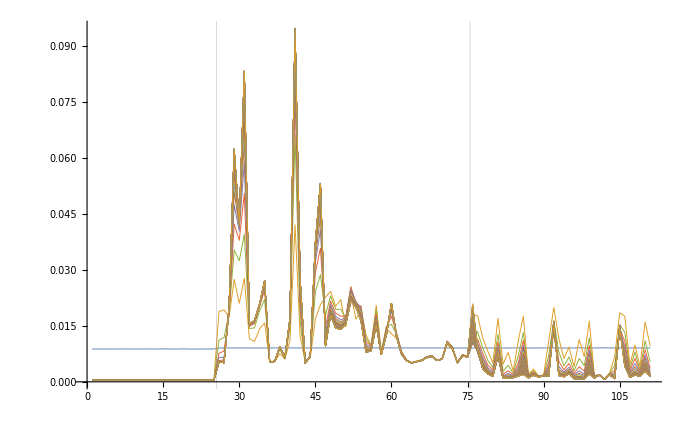

```mathematica
PhiEvolutionStatic["n2599-m275-k25-uc36-ic50-batch-hier-vb/"]
```

```mathematica
PhiEvolutionB["n2599-m275-k25-uc36-ic50-lfirst-fpriors/",90]
```

```mathematica
PhiEvolutionB["n2599-m275-k25-uc36-ic50-lfirst/",200]
```

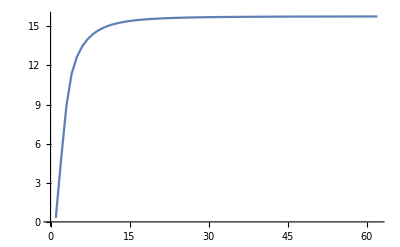

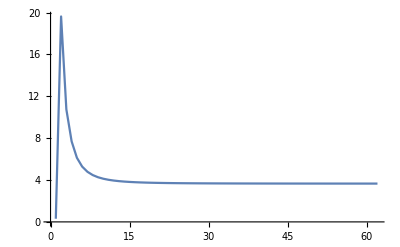

```mathematica
name="n2599-m275-k25-uc36-ic50-batch-hier-vb/";
dirOut="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/output/";
SetDirectory[dirOut<>name];
xiMeans=Import["xiMeans.tsv"];
ListPlot[xiMeans[[1;;62]]ᵀ,PlotRange->All,Joined->True]
name="n2599-m275-k25-uc36-ic50-batch-hier-vb/";
dirOut="~/Dropbox/2015_Summer/Athey/Matlab_AtheyCastillo/Yogurt/observables/output/";
SetDirectory[dirOut<>name];
etaMeans=Import["etaMeans.tsv"];
ListPlot[etaMeans[[1;;62]]ᵀ,PlotRange->All,Joined->True]
```

```mathematica
]
```

```mathematica
etaMeans
```

{{21.7355},{13.146},{15.3818},{11.9111},{9.38505},{8.05346},{7.40976},{7.07652},{6.89159},{6.78144},{6.7116},{6.6648},{6.63199},{6.60812},{6.59026},{6.57658},{6.5659},{6.55743},{6.55063},{6.54509},{6.54054},{6.53678},{6.53363},{6.53097},{6.52872},{6.52679},{6.52513},{6.52369},{6.52244},{6.52136},{6.52041},{6.51958},{6.51885},{6.51821},{6.51765},{6.51716},{6.51672},{6.51634},{6.516},{6.51569},{6.51541},{6.51516},{6.51493},{6.51473},{6.51455},{6.51439},{6.51425},{6.51413},{6.51403},{6.51394},{6.51387},{6.51381},{6.51376},{6.51372},{6.51369},{6.51366},{6.51363},{6.51361},{6.51359},{6.51357},{6.51355},{6.51354},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

```mathematica
200 3000
```

600000

```mathematica
3803-1229
```

2574

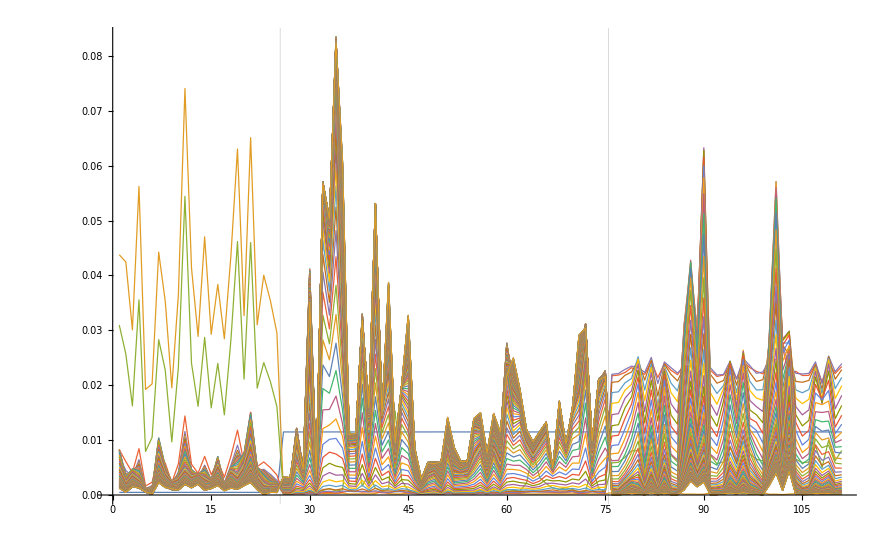

```mathematica
PhiEvolutionStatic["n2599-m275-k25-uc36-ic50-batch-hier-vb-lfirst/"]
```